# PME3380 - Rec

## Posições e velocidades

```mathematica
x1[t] = (L1/2)*Sin[alpha[t]];
y1[t] = -(L1/2)*Cos[alpha[t]];

x2[t] = L1*Sin[alpha[t]] + (L2/2)*Sin[beta[t]];
y2[t] = -L1*Cos[alpha[t]]- (L2/2)*Cos[beta[t]];

x3[t] =L1*Sin[alpha[t]] + L2*Sin[beta[t]];
y3[t] =-L1*Cos[alpha[t]]- L2*Cos[beta[t]];

x1'[t]=D[x1[t],t];
y1'[t]=D[y1[t],t];
x2'[t]=D[x2[t],t];
y2'[t]=D[y2[t],t];
x3'[t] =D[x3[t],t];
y3'[t]=D[y3[t],t];


v1[t]=Sqrt[x1'[t]^2+y1'[t]^2];
v2[t]=Sqrt[x2'[t]^2+y2'[t]^2];
v3[t]=Sqrt[x3'[t]^2+y3'[t]^2];
```

## Energia cinética

```mathematica
IG1 = (m1*L1^2)/12;
IG2 = (m2*L2^2)/12;
IG3 = (m3*L3^2)/12;
T1=1/2 m1*v1[t]^2+1/2*IG1*(alpha'[t])^2;
T2=1/2 m2*v2[t]^2+1/2*IG2*(beta'[t])^2;
T3=1/2 m3*v3[t]^2+ 1/2*IG3*(beta'[t])^2; 
T=T1+T2 +T3
```

1/24 L1^2 m1 alpha'[t]^2+1/2 m1 (1/4 L1^2 Cos[alpha[t]]^2 alpha'[t]^2+1/4 L1^2 Sin[alpha[t]]^2 alpha'[t]^2)+1/24 L2^2 m2 beta'[t]^2+1/24 L3^2 m3 beta'[t]^2+1/2 m2 ((L1 Cos[alpha[t]] alpha'[t]+1/2 L2 Cos[beta[t]] beta'[t])^2+(L1 Sin[alpha[t]] alpha'[t]+1/2 L2 Sin[beta[t]] beta'[t])^2)+1/2 m3 ((L1 Cos[alpha[t]] alpha'[t]+L2 Cos[beta[t]] beta'[t])^2+(L1 Sin[alpha[t]] alpha'[t]+L2 Sin[beta[t]] beta'[t])^2)

## Energia potencial

```mathematica
V1=m1*g*y1[t];
V2=m2*g*y2[t];
V3=m3*g*y3[t];
V=V1+V2 +V3
```

-1/2 g L1 m1 Cos[alpha[t]]+g m3 (-L1 Cos[alpha[t]]-L2 Cos[beta[t]])+g m2 (-L1 Cos[alpha[t]]-1/2 L2 Cos[beta[t]])

## Lagrange

```mathematica
L=T-V;
```

## Rayleigh

```mathematica
R= 1/2*c*(alpha'[t]-beta'[t])^2;
```

## Equações

```mathematica
eq1=D[D[L, alpha'[t]],t]-D[L, alpha[t]]+D[R, alpha'[t]](*Para alpha*)

eq2=D[D[L, beta'[t]],t]-D[L, beta[t]]+D[R, beta'[t]](*Para beta*)
```

1/2 g L1 m1 Sin[alpha[t]]+g L1 m2 Sin[alpha[t]]+g L1 m3 Sin[alpha[t]]+c (alpha'[t]-beta'[t])-1/2 m2 (-2 L1 Sin[alpha[t]] alpha'[t] (L1 Cos[alpha[t]] alpha'[t]+1/2 L2 Cos[beta[t]] beta'[t])+2 L1 Cos[alpha[t]] alpha'[t] (L1 Sin[alpha[t]] alpha'[t]+1/2 L2 Sin[beta[t]] beta'[t]))-1/2 m3 (-2 L1 Sin[alpha[t]] alpha'[t] (L1 Cos[alpha[t]] alpha'[t]+L2 Cos[beta[t]] beta'[t])+2 L1 Cos[alpha[t]] alpha'[t] (L1 Sin[alpha[t]] alpha'[t]+L2 Sin[beta[t]] beta'[t]))+1/12 L1^2 m1 alpha''[t]+1/2 m1 (1/2 L1^2 Cos[alpha[t]]^2 alpha''[t]+1/2 L1^2 Sin[alpha[t]]^2 alpha''[t])+1/2 m2 (-2 L1 Sin[alpha[t]] alpha'[t] (L1 Cos[alpha[t]] alpha'[t]+1/2 L2 Cos[beta[t]] beta'[t])+2 L1 Cos[alpha[t]] alpha'[t] (L1 Sin[alpha[t]] alpha'[t]+1/2 L2 Sin[beta[t]] beta'[t])+2 L1 Cos[alpha[t]] (-L1 Sin[alpha[t]] alpha'[t]^2-1/2 L2 Sin[beta[t]] beta'[t]^2+L1 Cos[alpha[t]] alpha''[t]+1/2 L2 Cos[beta[t]] beta''[t])+2 L1 Sin[alpha[t]] (L1 Cos[alpha[t]] alpha'[t]^2+1/2 L2 Cos[beta[t]] beta'[t]^2+L1 Sin[alpha[t]] alpha''[t]+1/2 L2 Sin[beta[t]] beta''[t]))+1/2 m3 (-2 L1 Sin[alpha[t]] alpha'[t] (L1 Cos[alpha[t]] alpha'[t]+L2 Cos[beta[t]] beta'[t])+2 L1 Cos[alpha[t]] alpha'[t] (L1 Sin[alpha[t]] alpha'[t]+L2 Sin[beta[t]] beta'[t])+2 L1 Cos[alpha[t]] (-L1 Sin[alpha[t]] alpha'[t]^2-L2 Sin[beta[t]] beta'[t]^2+L1 Cos[alpha[t]] alpha''[t]+L2 Cos[beta[t]] beta''[t])+2 L1 Sin[alpha[t]] (L1 Cos[alpha[t]] alpha'[t]^2+L2 Cos[beta[t]] beta'[t]^2+L1 Sin[alpha[t]] alpha''[t]+L2 Sin[beta[t]] beta''[t]))

1/2 g L2 m2 Sin[beta[t]]+g L2 m3 Sin[beta[t]]-c (alpha'[t]-beta'[t])-1/2 m2 (-L2 Sin[beta[t]] beta'[t] (L1 Cos[alpha[t]] alpha'[t]+1/2 L2 Cos[beta[t]] beta'[t])+L2 Cos[beta[t]] beta'[t] (L1 Sin[alpha[t]] alpha'[t]+1/2 L2 Sin[beta[t]] beta'[t]))-1/2 m3 (-2 L2 Sin[beta[t]] beta'[t] (L1 Cos[alpha[t]] alpha'[t]+L2 Cos[beta[t]] beta'[t])+2 L2 Cos[beta[t]] beta'[t] (L1 Sin[alpha[t]] alpha'[t]+L2 Sin[beta[t]] beta'[t]))+1/12 L2^2 m2 beta''[t]+1/12 L3^2 m3 beta''[t]+1/2 m2 (-L2 Sin[beta[t]] beta'[t] (L1 Cos[alpha[t]] alpha'[t]+1/2 L2 Cos[beta[t]] beta'[t])+L2 Cos[beta[t]] beta'[t] (L1 Sin[alpha[t]] alpha'[t]+1/2 L2 Sin[beta[t]] beta'[t])+L2 Cos[beta[t]] (-L1 Sin[alpha[t]] alpha'[t]^2-1/2 L2 Sin[beta[t]] beta'[t]^2+L1 Cos[alpha[t]] alpha''[t]+1/2 L2 Cos[beta[t]] beta''[t])+L2 Sin[beta[t]] (L1 Cos[alpha[t]] alpha'[t]^2+1/2 L2 Cos[beta[t]] beta'[t]^2+L1 Sin[alpha[t]] alpha''[t]+1/2 L2 Sin[beta[t]] beta''[t]))+1/2 m3 (-2 L2 Sin[beta[t]] beta'[t] (L1 Cos[alpha[t]] alpha'[t]+L2 Cos[beta[t]] beta'[t])+2 L2 Cos[beta[t]] beta'[t] (L1 Sin[alpha[t]] alpha'[t]+L2 Sin[beta[t]] beta'[t])+2 L2 Cos[beta[t]] (-L1 Sin[alpha[t]] alpha'[t]^2-L2 Sin[beta[t]] beta'[t]^2+L1 Cos[alpha[t]] alpha''[t]+L2 Cos[beta[t]] beta''[t])+2 L2 Sin[beta[t]] (L1 Cos[alpha[t]] alpha'[t]^2+L2 Cos[beta[t]] beta'[t]^2+L1 Sin[alpha[t]] alpha''[t]+L2 Sin[beta[t]] beta''[t]))

## Equações finais separadas

```mathematica
EL = {eq1 == 0,eq2 ==0};
Subs1={alpha[t]->Subscript[x, 1], beta[t]->Subscript[x, 2],alpha'[t]->Subscript[x, 3],beta'[t]->Subscript[x, 4]};
ELnl=EL;
PPnl=Solve[ELnl,{alpha''[t],beta''[t]}]//First;

𝕩[t]={Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t],Subscript[x, 4][t]};
𝕩'[t]={Subscript[x, 3][t],Subscript[x, 4][t],alpha''[t],beta''[t]};
EENL={D[𝕩[t],t]==𝕩'[t]/.PPnl[[1]]/.PPnl[[2]]};
TableForm[EENL]
```

{x_1'[t],x_2'[t],x_3'[t],x_4'[t]}=={x_3[t],x_4[t],-(-(((L2^2 m2)/12+(L3^2 m3)/12+1/4 L2^2 m2 Cos[beta[t]]^2+L2^2 m3 Cos[beta[t]]^2+1/4 L2^2 m2 Sin[beta[t]]^2+L2^2 m3 Sin[beta[t]]^2) (1/2 g L1 m1 Sin[alpha[t]]+g L1 m2 Sin[alpha[t]]+g L1 m3 Sin[alpha[t]]+c (alpha'[t]-beta'[t])+1/2 L1 L2 m2 Cos[beta[t]] Sin[alpha[t]] beta'[t]^2+L1 L2 m3 Cos[beta[t]] Sin[alpha[t]] beta'[t]^2-1/2 L1 L2 m2 Cos[alpha[t]] Sin[beta[t]] beta'[t]^2-L1 L2 m3 Cos[alpha[t]] Sin[beta[t]] beta'[t]^2-L1 m2 Sin[alpha[t]] alpha'[t] (L1 Cos[alpha[t]] alpha'[t]+1/2 L2 Cos[beta[t]] beta'[t])-L1 m3 Sin[alpha[t]] alpha'[t] (L1 Cos[alpha[t]] alpha'[t]+L2 Cos[beta[t]] beta'[t])+L1 m2 Cos[alpha[t]] alpha'[t] (L1 Sin[alpha[t]] alpha'[t]+1/2 L2 Sin[beta[t]] beta'[t])+L1 m3 Cos[alpha[t]] alpha'[t] (L1 Sin[alpha[t]] alpha'[t]+L2 Sin[beta[t]] beta'[t])-1/2 m2 (-2 L1 Sin[alpha[t]] alpha'[t] (L1 Cos[alpha[t]] alpha'[t]+1/2 L2 Cos[beta[t]] beta'[t])+2 L1 Cos[alpha[t]] alpha'[t] (L1 Sin[alpha[t]] alpha'[t]+1/2 L2 Sin[beta[t]] beta'[t]))-1/2 m3 (-2 L1 Sin[alpha[t]] alpha'[t] (L1 Cos[alpha[t]] alpha'[t]+L2 Cos[beta[t]] beta'[t])+2 L1 Cos[alpha[t]] alpha'[t] (L1 Sin[alpha[t]] alpha'[t]+L2 Sin[beta[t]] beta'[t]))))+(1/2 L1 L2 m2 Cos[alpha[t]] Cos[beta[t]]+L1 L2 m3 Cos[alpha[t]] Cos[beta[t]]+1/2 L1 L2 m2 Sin[alpha[t]] Sin[beta[t]]+L1 L2 m3 Sin[alpha[t]] Sin[beta[t]]) (1/2 g L2 m2 Sin[beta[t]]+g L2 m3 Sin[beta[t]]-1/2 L1 L2 m2 Cos[beta[t]] Sin[alpha[t]] alpha'[t]^2-L1 L2 m3 Cos[beta[t]] Sin[alpha[t]] alpha'[t]^2+1/2 L1 L2 m2 Cos[alpha[t]] Sin[beta[t]] alpha'[t]^2+L1 L2 m3 Cos[alpha[t]] Sin[beta[t]] alpha'[t]^2-c (alpha'[t]-beta'[t])-1/2 L2 m2 Sin[beta[t]] beta'[t] (L1 Cos[alpha[t]] alpha'[t]+1/2 L2 Cos[beta[t]] beta'[t])-L2 m3 Sin[beta[t]] beta'[t] (L1 Cos[alpha[t]] alpha'[t]+L2 Cos[beta[t]] beta'[t])+1/2 L2 m2 Cos[beta[t]] beta'[t] (L1 Sin[alpha[t]] alpha'[t]+1/2 L2 Sin[beta[t]] beta'[t])+L2 m3 Cos[beta[t]] beta'[t] (L1 Sin[alpha[t]] alpha'[t]+L2 Sin[beta[t]] beta'[t])-1/2 m2 (-L2 Sin[beta[t]] beta'[t] (L1 Cos[alpha[t]] alpha'[t]+1/2 L2 Cos[beta[t]] beta'[t])+L2 Cos[beta[t]] beta'[t] (L1 Sin[alpha[t]] alpha'[t]+1/2 L2 Sin[beta[t]] beta'[t]))-1/2 m3 (-2 L2 Sin[beta[t]] beta'[t] (L1 Cos[alpha[t]] alpha'[t]+L2 Cos[beta[t]] beta'[t])+2 L2 Cos[beta[t]] beta'[t] (L1 Sin[alpha[t]] alpha'[t]+L2 Sin[beta[t]] beta'[t]))))/((1/2 L1 L2 m2 Cos[alpha[t]] Cos[beta[t]]+L1 L2 m3 Cos[alpha[t]] Cos[beta[t]]+1/2 L1 L2 m2 Sin[alpha[t]] Sin[beta[t]]+L1 L2 m3 Sin[alpha[t]] Sin[beta[t]])^2-((L1^2 m1)/12+1/4 L1^2 m1 Cos[alpha[t]]^2+L1^2 m2 Cos[alpha[t]]^2+L1^2 m3 Cos[alpha[t]]^2+1/4 L1^2 m1 Sin[alpha[t]]^2+L1^2 m2 Sin[alpha[t]]^2+L1^2 m3 Sin[alpha[t]]^2) ((L2^2 m2)/12+(L3^2 m3)/12+1/4 L2^2 m2 Cos[beta[t]]^2+L2^2 m3 Cos[beta[t]]^2+1/4 L2^2 m2 Sin[beta[t]]^2+L2^2 m3 Sin[beta[t]]^2)),-(6 (-6 g L1 L2 m1 m2 Cos[alpha[t]] Cos[beta[t]] Sin[alpha[t]]-12 g L1 L2 m2^2 Cos[alpha[t]] Cos[beta[t]] Sin[alpha[t]]-12 g L1 L2 m1 m3 Cos[alpha[t]] Cos[beta[t]] Sin[alpha[t]]-36 g L1 L2 m2 m3 Cos[alpha[t]] Cos[beta[t]] Sin[alpha[t]]-24 g L1 L2 m3^2 Cos[alpha[t]] Cos[beta[t]] Sin[alpha[t]]+g L1 L2 m1 m2 Sin[beta[t]]+2 g L1 L2 m1 m3 Sin[beta[t]]+3 g L1 L2 m1 m2 Cos[alpha[t]]^2 Sin[beta[t]]+12 g L1 L2 m2^2 Cos[alpha[t]]^2 Sin[beta[t]]+6 g L1 L2 m1 m3 Cos[alpha[t]]^2 Sin[beta[t]]+36 g L1 L2 m2 m3 Cos[alpha[t]]^2 Sin[beta[t]]+24 g L1 L2 m3^2 Cos[alpha[t]]^2 Sin[beta[t]]-3 g L1 L2 m1 m2 Sin[alpha[t]]^2 Sin[beta[t]]-6 g L1 L2 m1 m3 Sin[alpha[t]]^2 Sin[beta[t]]-2 c L1 m1 alpha'[t]-6 c L1 m1 Cos[alpha[t]]^2 alpha'[t]-24 c L1 m2 Cos[alpha[t]]^2 alpha'[t]-24 c L1 m3 Cos[alpha[t]]^2 alpha'[t]-12 c L2 m2 Cos[alpha[t]] Cos[beta[t]] alpha'[t]-24 c L2 m3 Cos[alpha[t]] Cos[beta[t]] alpha'[t]-6 c L1 m1 Sin[alpha[t]]^2 alpha'[t]-24 c L1 m2 Sin[alpha[t]]^2 alpha'[t]-24 c L1 m3 Sin[alpha[t]]^2 alpha'[t]-12 c L2 m2 Sin[alpha[t]] Sin[beta[t]] alpha'[t]-24 c L2 m3 Sin[alpha[t]] Sin[beta[t]] alpha'[t]-L1^2 L2 m1 m2 Cos[beta[t]] Sin[alpha[t]] alpha'[t]^2-2 L1^2 L2 m1 m3 Cos[beta[t]] Sin[alpha[t]] alpha'[t]^2-3 L1^2 L2 m1 m2 Cos[alpha[t]]^2 Cos[beta[t]] Sin[alpha[t]] alpha'[t]^2-12 L1^2 L2 m2^2 Cos[alpha[t]]^2 Cos[beta[t]] Sin[alpha[t]] alpha'[t]^2-6 L1^2 L2 m1 m3 Cos[alpha[t]]^2 Cos[beta[t]] Sin[alpha[t]] alpha'[t]^2-36 L1^2 L2 m2 m3 Cos[alpha[t]]^2 Cos[beta[t]] Sin[alpha[t]] alpha'[t]^2-24 L1^2 L2 m3^2 Cos[alpha[t]]^2 Cos[beta[t]] Sin[alpha[t]] alpha'[t]^2-3 L1^2 L2 m1 m2 Cos[beta[t]] Sin[alpha[t]]^3 alpha'[t]^2-12 L1^2 L2 m2^2 Cos[beta[t]] Sin[alpha[t]]^3 alpha'[t]^2-6 L1^2 L2 m1 m3 Cos[beta[t]] Sin[alpha[t]]^3 alpha'[t]^2-36 L1^2 L2 m2 m3 Cos[beta[t]] Sin[alpha[t]]^3 alpha'[t]^2-24 L1^2 L2 m3^2 Cos[beta[t]] Sin[alpha[t]]^3 alpha'[t]^2+L1^2 L2 m1 m2 Cos[alpha[t]] Sin[beta[t]] alpha'[t]^2+2 L1^2 L2 m1 m3 Cos[alpha[t]] Sin[beta[t]] alpha'[t]^2+3 L1^2 L2 m1 m2 Cos[alpha[t]]^3 Sin[beta[t]] alpha'[t]^2+12 L1^2 L2 m2^2 Cos[alpha[t]]^3 Sin[beta[t]] alpha'[t]^2+6 L1^2 L2 m1 m3 Cos[alpha[t]]^3 Sin[beta[t]] alpha'[t]^2+36 L1^2 L2 m2 m3 Cos[alpha[t]]^3 Sin[beta[t]] alpha'[t]^2+24 L1^2 L2 m3^2 Cos[alpha[t]]^3 Sin[beta[t]] alpha'[t]^2+3 L1^2 L2 m1 m2 Cos[alpha[t]] Sin[alpha[t]]^2 Sin[beta[t]] alpha'[t]^2+12 L1^2 L2 m2^2 Cos[alpha[t]] Sin[alpha[t]]^2 Sin[beta[t]] alpha'[t]^2+6 L1^2 L2 m1 m3 Cos[alpha[t]] Sin[alpha[t]]^2 Sin[beta[t]] alpha'[t]^2+36 L1^2 L2 m2 m3 Cos[alpha[t]] Sin[alpha[t]]^2 Sin[beta[t]] alpha'[t]^2+24 L1^2 L2 m3^2 Cos[alpha[t]] Sin[alpha[t]]^2 Sin[beta[t]] alpha'[t]^2+2 c L1 m1 beta'[t]+6 c L1 m1 Cos[alpha[t]]^2 beta'[t]+24 c L1 m2 Cos[alpha[t]]^2 beta'[t]+24 c L1 m3 Cos[alpha[t]]^2 beta'[t]+12 c L2 m2 Cos[alpha[t]] Cos[beta[t]] beta'[t]+24 c L2 m3 Cos[alpha[t]] Cos[beta[t]] beta'[t]+6 c L1 m1 Sin[alpha[t]]^2 beta'[t]+24 c L1 m2 Sin[alpha[t]]^2 beta'[t]+24 c L1 m3 Sin[alpha[t]]^2 beta'[t]+12 c L2 m2 Sin[alpha[t]] Sin[beta[t]] beta'[t]+24 c L2 m3 Sin[alpha[t]] Sin[beta[t]] beta'[t]-6 L1 L2^2 m2^2 Cos[alpha[t]] Cos[beta[t]]^2 Sin[alpha[t]] beta'[t]^2-24 L1 L2^2 m2 m3 Cos[alpha[t]] Cos[beta[t]]^2 Sin[alpha[t]] beta'[t]^2-24 L1 L2^2 m3^2 Cos[alpha[t]] Cos[beta[t]]^2 Sin[alpha[t]] beta'[t]^2+6 L1 L2^2 m2^2 Cos[alpha[t]]^2 Cos[beta[t]] Sin[beta[t]] beta'[t]^2+24 L1 L2^2 m2 m3 Cos[alpha[t]]^2 Cos[beta[t]] Sin[beta[t]] beta'[t]^2+24 L1 L2^2 m3^2 Cos[alpha[t]]^2 Cos[beta[t]] Sin[beta[t]] beta'[t]^2-6 L1 L2^2 m2^2 Cos[beta[t]] Sin[alpha[t]]^2 Sin[beta[t]] beta'[t]^2-24 L1 L2^2 m2 m3 Cos[beta[t]] Sin[alpha[t]]^2 Sin[beta[t]] beta'[t]^2-24 L1 L2^2 m3^2 Cos[beta[t]] Sin[alpha[t]]^2 Sin[beta[t]] beta'[t]^2+6 L1 L2^2 m2^2 Cos[alpha[t]] Sin[alpha[t]] Sin[beta[t]]^2 beta'[t]^2+24 L1 L2^2 m2 m3 Cos[alpha[t]] Sin[alpha[t]] Sin[beta[t]]^2 beta'[t]^2+24 L1 L2^2 m3^2 Cos[alpha[t]] Sin[alpha[t]] Sin[beta[t]]^2 beta'[t]^2))/(L1 (L2^2 m1 m2+L3^2 m1 m3+3 L2^2 m1 m2 Cos[alpha[t]]^2+12 L2^2 m2^2 Cos[alpha[t]]^2+3 L3^2 m1 m3 Cos[alpha[t]]^2+12 L2^2 m2 m3 Cos[alpha[t]]^2+12 L3^2 m2 m3 Cos[alpha[t]]^2+12 L3^2 m3^2 Cos[alpha[t]]^2+3 L2^2 m1 m2 Cos[beta[t]]^2+12 L2^2 m1 m3 Cos[beta[t]]^2+9 L2^2 m1 m2 Cos[alpha[t]]^2 Cos[beta[t]]^2+36 L2^2 m1 m3 Cos[alpha[t]]^2 Cos[beta[t]]^2+36 L2^2 m2 m3 Cos[alpha[t]]^2 Cos[beta[t]]^2+3 L2^2 m1 m2 Sin[alpha[t]]^2+12 L2^2 m2^2 Sin[alpha[t]]^2+3 L3^2 m1 m3 Sin[alpha[t]]^2+12 L2^2 m2 m3 Sin[alpha[t]]^2+12 L3^2 m2 m3 Sin[alpha[t]]^2+12 L3^2 m3^2 Sin[alpha[t]]^2+9 L2^2 m1 m2 Cos[beta[t]]^2 Sin[alpha[t]]^2+36 L2^2 m2^2 Cos[beta[t]]^2 Sin[alpha[t]]^2+36 L2^2 m1 m3 Cos[beta[t]]^2 Sin[alpha[t]]^2+180 L2^2 m2 m3 Cos[beta[t]]^2 Sin[alpha[t]]^2+144 L2^2 m3^2 Cos[beta[t]]^2 Sin[alpha[t]]^2-72 L2^2 m2^2 Cos[alpha[t]] Cos[beta[t]] Sin[alpha[t]] Sin[beta[t]]-288 L2^2 m2 m3 Cos[alpha[t]] Cos[beta[t]] Sin[alpha[t]] Sin[beta[t]]-288 L2^2 m3^2 Cos[alpha[t]] Cos[beta[t]] Sin[alpha[t]] Sin[beta[t]]+3 L2^2 m1 m2 Sin[beta[t]]^2+12 L2^2 m1 m3 Sin[beta[t]]^2+9 L2^2 m1 m2 Cos[alpha[t]]^2 Sin[beta[t]]^2+36 L2^2 m2^2 Cos[alpha[t]]^2 Sin[beta[t]]^2+36 L2^2 m1 m3 Cos[alpha[t]]^2 Sin[beta[t]]^2+180 L2^2 m2 m3 Cos[alpha[t]]^2 Sin[beta[t]]^2+144 L2^2 m3^2 Cos[alpha[t]]^2 Sin[beta[t]]^2+9 L2^2 m1 m2 Sin[alpha[t]]^2 Sin[beta[t]]^2+36 L2^2 m1 m3 Sin[alpha[t]]^2 Sin[beta[t]]^2+36 L2^2 m2 m3 Sin[alpha[t]]^2 Sin[beta[t]]^2))}

```mathematica
EQ3=Simplify[𝕩'[t][[3]]/.PPnl[[1]]/.PPnl[[2]]]

EQ4=Simplify[𝕩'[t][[4]]/.PPnl[[1]]/.PPnl[[2]]]
```

-((3 (g L1 ((L3^2 m3 (m1+2 (m2+m3))+L2^2 (5 m2^2+20 m2 m3+12 m3^2+4 m1 (m2+3 m3))) Sin[alpha[t]]+3 L2^2 (m2+2 m3)^2 Sin[alpha[t]-2 beta[t]])+2 c (L3^2 m3+4 L2^2 (m2+3 m3)+6 L1 L2 (m2+2 m3) Cos[alpha[t]-beta[t]]) alpha'[t]+3 L1^2 L2^2 (m2+2 m3)^2 Sin[2 (alpha[t]-beta[t])] alpha'[t]^2-2 c (L3^2 m3+4 L2^2 (m2+3 m3)+6 L1 L2 (m2+2 m3) Cos[alpha[t]-beta[t]]) beta'[t]+L1 L2 (m2+2 m3) (L3^2 m3+4 L2^2 (m2+3 m3)) Sin[alpha[t]-beta[t]] beta'[t]^2))/(L1^2 (2 L3^2 m3 (m1+3 (m2+m3))+L2^2 (15 m2^2+60 m2 m3+36 m3^2+8 m1 (m2+3 m3))-9 L2^2 (m2+2 m3)^2 Cos[2 (alpha[t]-beta[t])])))

(3 (g L1 L2 (m2+2 m3) (3 (m1+2 (m2+m3)) Sin[2 alpha[t]-beta[t]]-(m1+6 (m2+m3)) Sin[beta[t]])+4 c (2 L1 (m1+3 (m2+m3))+3 L2 (m2+2 m3) Cos[alpha[t]-beta[t]]) alpha'[t]+4 L1^2 L2 (m2+2 m3) (m1+3 (m2+m3)) Sin[alpha[t]-beta[t]] alpha'[t]^2-4 c (2 L1 (m1+3 (m2+m3))+3 L2 (m2+2 m3) Cos[alpha[t]-beta[t]]) beta'[t]+3 L1 L2^2 (m2+2 m3)^2 Sin[2 (alpha[t]-beta[t])] beta'[t]^2))/(L1 (2 L3^2 m3 (m1+3 (m2+m3))+L2^2 (15 m2^2+60 m2 m3+36 m3^2+8 m1 (m2+3 m3))-9 L2^2 (m2+2 m3)^2 Cos[2 (alpha[t]-beta[t])]))

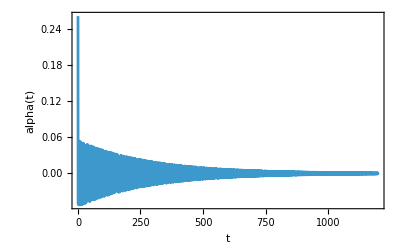

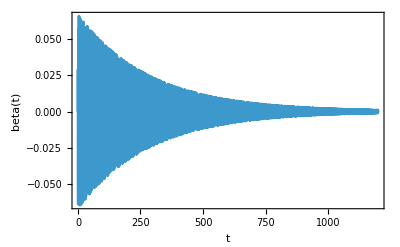

```mathematica
m1= 3;
m2=0.4;
m3=60;
g=9.81;
L1=0.25;
L2=0.65;
L3=1.2;
c=10;
F =10;
tend =1200;
NumSolution1=NDSolve[{alpha''[t]==EQ3,beta''[t]==EQ4,alpha[0]==0.261799,alpha'[0]==0,beta[0]==0,beta'[0]==0},{alpha,beta},{t,0,tend}];


Plot[Evaluate[alpha[t]/.NumSolution1],{t,0,1200},FrameLabel->{t,alpha[t]},DisplayFunction->Identity,Axes->False,Frame->True,PlotRange->All]

Plot[Evaluate[beta[t]/.NumSolution1],{t,0,1200},FrameLabel->{t,beta[t]},DisplayFunction->Identity,Axes->False,Frame->True,PlotRange->All]
```

```mathematica
Quit
```